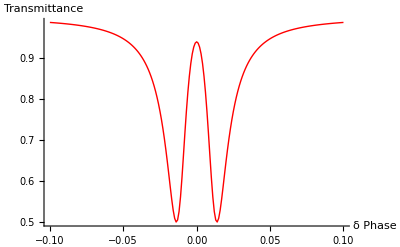

```mathematica
Etrans:=(r1-r12*a1*Exp[I ϕ1])/(1-r1 *r12*a1*Exp[I ϕ1])
r12:=(r2-a2*Exp[I ϕ2])/(1-r2*a2*Exp[I ϕ2])
a1:=Exp[(-α1*L1)/2]
a2:=Exp[(-α2*L2)/2]
α1:=(2*Pi*n)/(Q1*λ)
α2:=(2*Pi*n)/(Q2*λ)
 ϕ2:= ϕ1
n:=3.45
Q1:=10^5
Q2:=10^6
λ:=1550*10^-9
L1:=2*Pi*5*10^-6
L2:=2*Pi*5*10^-6
r1:=0.986
r2:=0.9999
ans:=Table[{ϕ1,Abs[Etrans]^2}, {ϕ1,-0.1,0.1,0.001}]
ans;
ListLinePlot[ans,PlotRange->All,AxesLabel->{ Phase  δ,Transmittance},LabelStyle->Directive[Black,Bold], PlotStyle->{Red,Thick}]
```